# 2-loop electron self-enegery with IREG

## Overlapping Diagram

## FeynCalc with FeynArts and TARCER

```mathematica
(*Load FeynCalc with FeynArts and the package TARCER*)
```

```mathematica
description="Electron self-energy at 2-loop with IREG-Overlapping Diagram";
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"TARCER","FeynArts"};
Get["FeynCalc`"]
$FAVerbose=0;
FCCheckVersion[9,3,0];
$Comment=True;
Off[General::"spell"];
Off[General::"spell1"];
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

TARCER 2.0, for more information see the accompanying publication. If you use TARCER in your research, please cite

• R. Mertig and R. Scharf, Comput. Phys. Commun., 111, 265-273, 1998, arXiv:hep-ph/9801383

FeynArts 3.11 (3 Aug 2020) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

## Fermion to Fermion process defined

```mathematica
ClearProcess[];
Processee={F[2,{1}]}->{F[2,{1}]};
SetOptions[InsertFields,InsertionLevel->{Particles},Model->FileNameJoin[{"QED","QED"}],GenericModel->FileNameJoin[{"QED","QED"}],ExcludeParticles->{F[2,{2|3}]}];
```

## Topology Generation with FeynArts

```mathematica
(*Topology creation with FeynArts function CreateTopologies[]. 1PI 2-loop topology for a 1->1 fermion (F[2,{1}]) process is generated. Default options for FeynArts function InsertFields[] are set*)
```

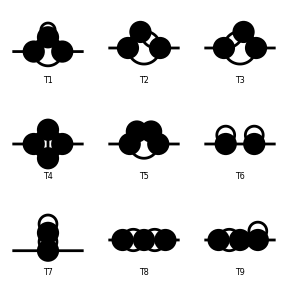

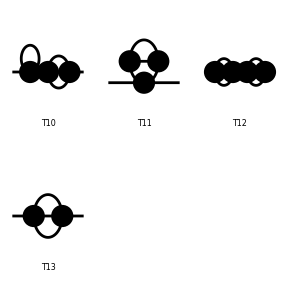

```mathematica
Topologiesfermions=CreateTopologies[2,1->1,ExcludeTopologies->{Tadpoles}];
Paint[Topologiesfermions];
```

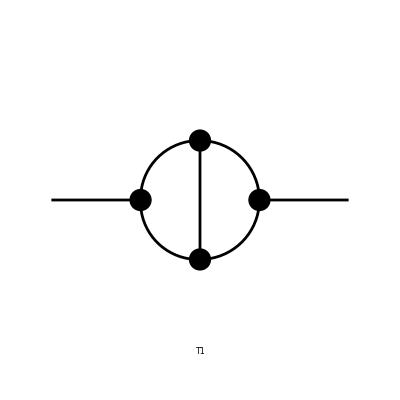

FeynArtsGraphics(1→1)(([T1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
overlappedtopology=Take[Topologiesfermions,{4}];
Paint[overlappedtopology]
```

## Diagram generation with fields

```mathematica
(*We substitute the propagators and external fields from QED in previous selected topology*)
```

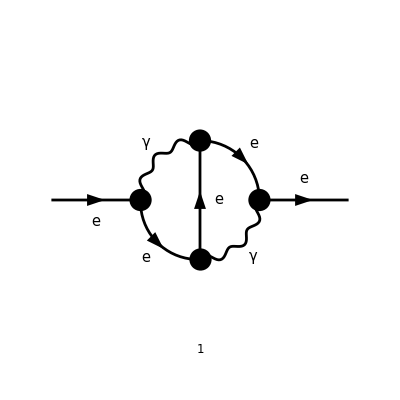

```mathematica
overlappedWITHfields=InsertFields[overlappedtopology,Processee,ExcludeParticles->{S[_],V[2|3],(S|U)[_],F[3|4],F[2,{2|3}]}];
Paint[overlappedWITHfields,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
```

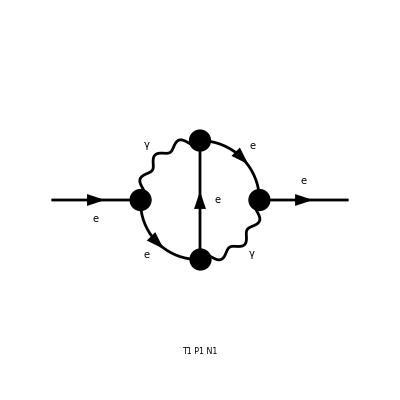

FeynArtsGraphics({e}→{e})(([T1 P1 N1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
theoverlappedcontribution=DiagramExtract[overlappedWITHfields,1];
Paint[theoverlappedcontribution]
```

## Amplitude (no regularized)

```mathematica
(*Amplitude is generated in FeynArts with function CreateFeynAmp[]. This expression is later conver to FeynCalc using FCFAConvert[]. Feynman gauge Subscript[ξ, g]=1 is chose later*)
```

```mathematica
FAamplElectronB=CreateFeynAmp[theoverlappedcontribution,Truncated->True,GaugeRules->{},PreFactor->1];
```

### In 4-dim (for IREG integrals)

```mathematica
(*Notice that we set in FCFAConvert options that ChangeDimensions->4*)
```

```mathematica
convertamplElectronB2=FCFAConvert[FAamplElectronB,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{l,k},LorentzIndexNames->{μ,ν,α,β},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,DropSumOver->True,Contract->True];
```

```mathematica
(*We work now in Feynman gauge*)
```

```mathematica
FeynmangaugeamplElectronB2=convertamplElectronB2/. GaugeXi[V[1]] -> 1
```

(ⅈ e^4 (γ̄)^ν.(γ̄·(p̄-k̄)+m_e).(γ̄)^β.(γ̄·(-k̄-l̄)+m_e).(γ̄)^ν.(m_e-γ̄·l̄).(γ̄)^β)/(((l̄)^2-m_e^2).(k̄)^2.((k̄+l̄)^2-m_e^2).((k̄-p̄)^2-m_e^2).(l̄+p̄)^2)

## Working in the massless regime

```mathematica
(*To compute the counterterm of the electron field, we set the mass zero in the amplitude before doing the simplification of Dirac matrices*)
```

```mathematica
MasslessOverlapped=FeynmangaugeamplElectronB2//.SMP["m_e"]->0
```

(ⅈ e^4 (γ̄)^ν.(γ̄·(p̄-k̄)).(γ̄)^β.(γ̄·(-k̄-l̄)).(γ̄)^ν.(-(γ̄·l̄)).(γ̄)^β)/((l̄)^2.(k̄)^2.(k̄+l̄)^2.(k̄-p̄)^2.(l̄+p̄)^2)

```mathematica
$PrePrint=FeynCalcForm;
```

```mathematica
SetOptions[$FrontEndSession,Evaluate[(Options[$FrontEndSession,"CommonDefaultFormatTypes"]/.("Output"->_)->("Output"->OutputForm))[[1]]]];
```

```mathematica
Print[MasslessOverlapped]
```

I DiracGamma[LorentzIndex[ν]] . DiracGamma[Momentum[-k + p]] . 
 
      DiracGamma[LorentzIndex[β]] . DiracGamma[Momentum[-k - l]] . 
 
      DiracGamma[LorentzIndex[ν]] . (-DiracGamma[Momentum[l]]) . 
 
      DiracGamma[LorentzIndex[β]] 
 
     FeynAmpDenominator[PropagatorDenominator[Momentum[l], 0], 
 
      PropagatorDenominator[Momentum[k], 0], 
 
      PropagatorDenominator[Momentum[k + l], 0], 
 
      PropagatorDenominator[Momentum[k - p], 0], 
 
                                                       4
      PropagatorDenominator[Momentum[l + p], 0]] SMP[e]

```mathematica
$PrePrint=.;
```

```mathematica
SetOptions[$FrontEndSession,Evaluate[(Options[$FrontEndSession,"CommonDefaultFormatTypes"]/.("Output"->_)->("Output"->TraditionalForm))[[1]]]];
```

```mathematica
(*Let's define then the general shift l->-l for each part*)
```

```mathematica
(*This is to have same denominator as Dias and Adriano in the beta paper*)
```

```mathematica
Print[MasslessOverlapped]
```

(ⅈ e^4 (γ̄)^ν.(γ̄·(p̄-k̄)).(γ̄)^β.(γ̄·(-k̄-l̄)).(γ̄)^ν.(-(γ̄·l̄)).(γ̄)^β)/((l̄)^2.(k̄)^2.(k̄+l̄)^2.(k̄-p̄)^2.(l̄+p̄)^2)

```mathematica
Shift1={DiracGamma[Momentum[-k-l]]->(DiracGamma[Momentum[-k+l]])};
Shift2={-DiracGamma[Momentum[l]]->DiracGamma[Momentum[l]]};
Shift3={Momentum[k+l]->Momentum[k-l]};
Shift4={Momentum[l+p]->Momentum[l-p]};
```

```mathematica
(*Sadly, in a define the general shift l->-l in separated parts because if not I have conflicts with the substitution after*)
```

```mathematica
Test=MasslessOverlapped//.Shift1;
Test2=Test//.Shift2;
Test3=Test2//.Shift3;
Test4=Test3//.Shift4
```

(ⅈ e^4 (γ̄)^ν.(γ̄·(p̄-k̄)).(γ̄)^β.(γ̄·(l̄-k̄)).(γ̄)^ν.(γ̄·l̄).(γ̄)^β)/((l̄)^2.(k̄)^2.(k̄-l̄)^2.(k̄-p̄)^2.(l̄-p̄)^2)

```mathematica
AlgebraDiracElectronB2Amassless=DiracSimplify[Test4]
```

-(8 ⅈ e^4 γ̄·k̄ (k̄·l̄))/((l̄)^2.(k̄)^2.(k̄-l̄)^2.(k̄-p̄)^2.(l̄-p̄)^2)+(8 ⅈ e^4 (k̄·l̄) γ̄·l̄)/((l̄)^2.(k̄)^2.(k̄-l̄)^2.(k̄-p̄)^2.(l̄-p̄)^2)+(8 ⅈ e^4 γ̄·k̄ (l̄·p̄))/((l̄)^2.(k̄)^2.(k̄-l̄)^2.(k̄-p̄)^2.(l̄-p̄)^2)-(8 ⅈ e^4 γ̄·l̄ (l̄·p̄))/((l̄)^2.(k̄)^2.(k̄-l̄)^2.(k̄-p̄)^2.(l̄-p̄)^2)

```mathematica
AlgebraDiracElectronC2Amassless=DiracSimplify[AlgebraDiracElectronB2Amassless]
```

-(8 ⅈ e^4 γ̄·k̄ (k̄·l̄))/((l̄)^2.(k̄)^2.(k̄-l̄)^2.(k̄-p̄)^2.(l̄-p̄)^2)+(8 ⅈ e^4 (k̄·l̄) γ̄·l̄)/((l̄)^2.(k̄)^2.(k̄-l̄)^2.(k̄-p̄)^2.(l̄-p̄)^2)+(8 ⅈ e^4 γ̄·k̄ (l̄·p̄))/((l̄)^2.(k̄)^2.(k̄-l̄)^2.(k̄-p̄)^2.(l̄-p̄)^2)-(8 ⅈ e^4 γ̄·l̄ (l̄·p̄))/((l̄)^2.(k̄)^2.(k̄-l̄)^2.(k̄-p̄)^2.(l̄-p̄)^2)

### Integrals for massless amplitude

```mathematica
{irrelevantmasslessIREG,loopsmassless,THEUNIQUEIREGINTEGRALSmassless}=FCLoopExtract[AlgebraDiracElectronC2Amassless,{l,k},loopHeadIREGmassless];
IREGINTEGRALSEBmassless=THEUNIQUEIREGINTEGRALSmassless/.loopHeadIREGmassless->Identity
```

{(γ̄·k̄ (k̄·l̄))/((k̄)^2.(l̄)^2.(l̄-p̄)^2.(k̄-p̄)^2.(k̄-l̄)^2),((k̄·l̄) γ̄·l̄)/((k̄)^2.(l̄)^2.(l̄-p̄)^2.(k̄-p̄)^2.(k̄-l̄)^2),(γ̄·k̄ (l̄·p̄))/((k̄)^2.(l̄)^2.(l̄-p̄)^2.(k̄-p̄)^2.(k̄-l̄)^2),(γ̄·l̄ (l̄·p̄))/((k̄)^2.(l̄)^2.(l̄-p̄)^2.(k̄-p̄)^2.(k̄-l̄)^2)}

## Replacements

```mathematica
(*First, we want to change the printed output to a an easy-to-read form. $PrePrint=FeynCalcForm forces displaying everything after applying FeynCalcForm*)
```

```mathematica
$PrePrint=FeynCalcForm;
```

```mathematica
SetOptions[$FrontEndSession,Evaluate[(Options[$FrontEndSession,"CommonDefaultFormatTypes"]/.("Output"->_)->("Output"->OutputForm))[[1]]]];
```

```mathematica
Print[AlgebraDiracElectronC2Amassless]
```

(-8 I) DiracGamma[Momentum[k]] FeynAmpDenominator[PropagatorDenominator[
 
        Momentum[l], 0], PropagatorDenominator[Momentum[k], 0], 
 
       PropagatorDenominator[Momentum[k - l], 0], 
 
       PropagatorDenominator[Momentum[k - p], 0], 
 
       PropagatorDenominator[Momentum[l - p], 0]] Pair[Momentum[k], Momentum[l]] 
 
            4
      SMP[e]  + (8 I) DiracGamma[Momentum[l]] 
 
      FeynAmpDenominator[PropagatorDenominator[Momentum[l], 0], 
 
       PropagatorDenominator[Momentum[k], 0], 
 
       PropagatorDenominator[Momentum[k - l], 0], 
 
       PropagatorDenominator[Momentum[k - p], 0], 
 
       PropagatorDenominator[Momentum[l - p], 0]] Pair[Momentum[k], Momentum[l]] 
 
            4
      SMP[e]  + (8 I) DiracGamma[Momentum[k]] 
 
      FeynAmpDenominator[PropagatorDenominator[Momentum[l], 0], 
 
       PropagatorDenominator[Momentum[k], 0], 
 
       PropagatorDenominator[Momentum[k - l], 0], 
 
       PropagatorDenominator[Momentum[k - p], 0], 
 
       PropagatorDenominator[Momentum[l - p], 0]] Pair[Momentum[l], Momentum[p]] 
 
            4
      SMP[e]  - (8 I) DiracGamma[Momentum[l]] 
 
      FeynAmpDenominator[PropagatorDenominator[Momentum[l], 0], 
 
       PropagatorDenominator[Momentum[k], 0], 
 
       PropagatorDenominator[Momentum[k - l], 0], 
 
       PropagatorDenominator[Momentum[k - p], 0], 
 
       PropagatorDenominator[Momentum[l - p], 0]] Pair[Momentum[l], Momentum[p]] 
 
            4
      SMP[e]

```mathematica
(*In order to change to the normal (internal) Mathematica OutputForm, we do:($PrePrint=.)*)
```

```mathematica
$PrePrint=.;
```

```mathematica
SetOptions[$FrontEndSession,Evaluate[(Options[$FrontEndSession,"CommonDefaultFormatTypes"]/.("Output"->_)->("Output"->TraditionalForm))[[1]]]];
```

```mathematica
Print[AlgebraDiracElectronC2Amassless]
```

-(8 ⅈ e^4 γ̄·k̄ (k̄·l̄))/((l̄)^2.(k̄)^2.(k̄-l̄)^2.(k̄-p̄)^2.(l̄-p̄)^2)+(8 ⅈ e^4 (k̄·l̄) γ̄·l̄)/((l̄)^2.(k̄)^2.(k̄-l̄)^2.(k̄-p̄)^2.(l̄-p̄)^2)+(8 ⅈ e^4 γ̄·k̄ (l̄·p̄))/((l̄)^2.(k̄)^2.(k̄-l̄)^2.(k̄-p̄)^2.(l̄-p̄)^2)-(8 ⅈ e^4 γ̄·l̄ (l̄·p̄))/((l̄)^2.(k̄)^2.(k̄-l̄)^2.(k̄-p̄)^2.(l̄-p̄)^2)

#### “Integral” list for the 2-loop overlapped diagram (massless case)

```mathematica
(*All the next terms corresponds to the integrals to be resolved in each of the previous un-regularized amplitudes*)
```

```mathematica
(*The

(∫_(-∞))^(+∞)(d^4 k)/(2π)^4(∫_(-∞))^(+∞)(d^4 l)/(2π)^4

 is implicit *)
```

```mathematica
TermC=DiracGamma[Momentum[k]]FeynAmpDenominator[PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[k],0],PropagatorDenominator[Momentum[k-l],0],PropagatorDenominator[Momentum[k-p],0],PropagatorDenominator[Momentum[l-p],0]]Pair[Momentum[l],Momentum[p]]
```

(γ̄·k̄ (l̄·p̄))/((l̄)^2.(k̄)^2.(k̄-l̄)^2.(k̄-p̄)^2.(l̄-p̄)^2)

```mathematica
TermE=DiracGamma[Momentum[l]]FeynAmpDenominator[PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[k],0],PropagatorDenominator[Momentum[k-l],0],PropagatorDenominator[Momentum[k-p],0],PropagatorDenominator[Momentum[l-p],0]]Pair[Momentum[l],Momentum[p]]
```

(γ̄·l̄ (l̄·p̄))/((l̄)^2.(k̄)^2.(k̄-l̄)^2.(k̄-p̄)^2.(l̄-p̄)^2)

```mathematica
TermG=DiracGamma[Momentum[l]]FeynAmpDenominator[PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[k],0],PropagatorDenominator[Momentum[k-l],0],PropagatorDenominator[Momentum[k-p],0],PropagatorDenominator[Momentum[l-p],0]]Pair[Momentum[k],Momentum[l]]
```

((k̄·l̄) γ̄·l̄)/((l̄)^2.(k̄)^2.(k̄-l̄)^2.(k̄-p̄)^2.(l̄-p̄)^2)

```mathematica
TermG2=DiracGamma[Momentum[k]] FeynAmpDenominator[PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[k],0],PropagatorDenominator[Momentum[k-l],0],PropagatorDenominator[Momentum[k-p],0],PropagatorDenominator[Momentum[l-p],0]]Pair[Momentum[k],Momentum[l]]
```

(γ̄·k̄ (k̄·l̄))/((l̄)^2.(k̄)^2.(k̄-l̄)^2.(k̄-p̄)^2.(l̄-p̄)^2)

### Integral results (massless case)

```mathematica
(*What I computed by hand*)
```

```mathematica
CRevisedReplace=b*(DiracGamma[Momentum[p]]/4)Ilogλ2
```

1/4 b Ilogλ2 γ̄·p̄

```mathematica
ERevisedReplace=DiracGamma[Momentum[p]]/4*Ilogλ2^2-DiracGamma[Momentum[p]]/4*b*Ilog2λ2+(9*DiracGamma[Momentum[p]])/8 b*Ilogλ2-DiracGamma[Momentum[p]]/4*b*Ilogλ2*Log[-p^2/λ^2]
```

-1/4 b Ilog2λ2 γ̄·p̄-1/4 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄+9/8 b Ilogλ2 γ̄·p̄+1/4 Ilogλ2^2 γ̄·p̄

```mathematica
GRevisedReplace=+DiracGamma[Momentum[p]]/8 Ilogλ2^2-(b*DiracGamma[Momentum[p]])/8 Ilog2λ2+(19*b*DiracGamma[Momentum[p]])/16*Ilogλ2-(b*DiracGamma[Momentum[p]])/8*Ilogλ2*Log[-p^2/λ^2]
```

-1/8 b Ilog2λ2 γ̄·p̄-1/8 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄+19/16 b Ilogλ2 γ̄·p̄+1/8 Ilogλ2^2 γ̄·p̄

```mathematica
G2RevisedReplace=+DiracGamma[Momentum[p]]/8 Ilogλ2^2-(b*DiracGamma[Momentum[p]])/8 Ilog2λ2+(19*b*DiracGamma[Momentum[p]])/16*Ilogλ2-(b*DiracGamma[Momentum[p]])/8*Ilogλ2*Log[-p^2/λ^2]
```

-1/8 b Ilog2λ2 γ̄·p̄-1/8 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄+19/16 b Ilogλ2 γ̄·p̄+1/8 Ilogλ2^2 γ̄·p̄

### Substitution rule for Mathematica

```mathematica
SubRule={TermG2->G2RevisedReplace,TermG->GRevisedReplace,TermC->CRevisedReplace,TermE->ERevisedReplace}
```

{(γ̄·k̄ (k̄·l̄))/((l̄)^2.(k̄)^2.(k̄-l̄)^2.(k̄-p̄)^2.(l̄-p̄)^2)→-1/8 b Ilog2λ2 γ̄·p̄-1/8 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄+19/16 b Ilogλ2 γ̄·p̄+1/8 Ilogλ2^2 γ̄·p̄,((k̄·l̄) γ̄·l̄)/((l̄)^2.(k̄)^2.(k̄-l̄)^2.(k̄-p̄)^2.(l̄-p̄)^2)→-1/8 b Ilog2λ2 γ̄·p̄-1/8 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄+19/16 b Ilogλ2 γ̄·p̄+1/8 Ilogλ2^2 γ̄·p̄,(γ̄·k̄ (l̄·p̄))/((l̄)^2.(k̄)^2.(k̄-l̄)^2.(k̄-p̄)^2.(l̄-p̄)^2)→1/4 b Ilogλ2 γ̄·p̄,(γ̄·l̄ (l̄·p̄))/((l̄)^2.(k̄)^2.(k̄-l̄)^2.(k̄-p̄)^2.(l̄-p̄)^2)→-1/4 b Ilog2λ2 γ̄·p̄-1/4 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄+9/8 b Ilogλ2 γ̄·p̄+1/4 Ilogλ2^2 γ̄·p̄}

### Regulated Amplitud with IREG (massless case)

```mathematica
RegulatedAmplitude=AlgebraDiracElectronC2Amassless//.SubRule
```

2 ⅈ b e^4 Ilogλ2 γ̄·p̄-8 ⅈ e^4 (-1/4 b Ilog2λ2 γ̄·p̄-1/4 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄+9/8 b Ilogλ2 γ̄·p̄+1/4 Ilogλ2^2 γ̄·p̄)

```mathematica
RegulatedEOverlappedAmplitudeIREG=Simplify[RegulatedAmplitude]
```

ⅈ e^4 γ̄·p̄ (2 b Ilog2λ2+2 b Ilogλ2 log(-p^2/λ^2)-7 b Ilogλ2-2 Ilogλ2^2)

### All counter-term part

#### Topology and diagrams

```mathematica
(*Topology creation*)
```

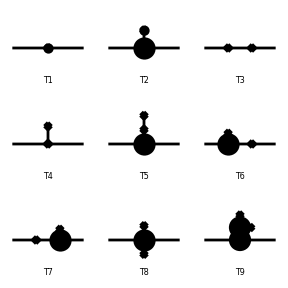

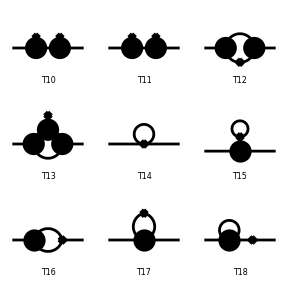

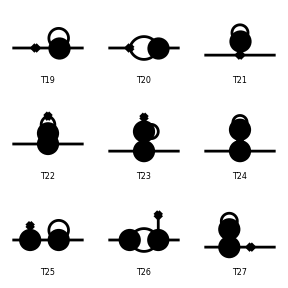

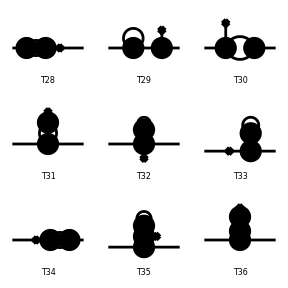

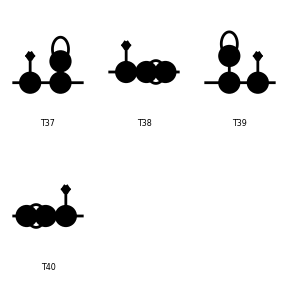

```mathematica
Topology1LoopFermionicSelfEnergyCorrection=CreateCTTopologies[2,1->1];
Paint[Topology1LoopFermionicSelfEnergyCorrection];
```

```mathematica
OverlappedCorrectionA=Take[Topology1LoopFermionicSelfEnergyCorrection,{16}];
```

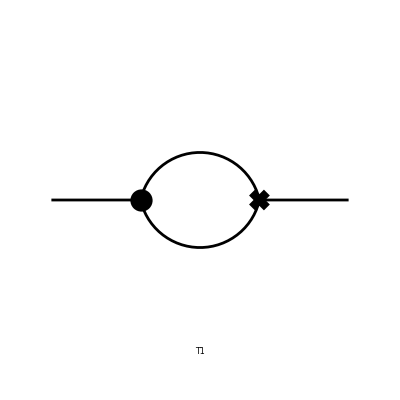

FeynArtsGraphics(1→1)(([T1] | Null | Null
Null | Null | Null
Null | Null | Null))

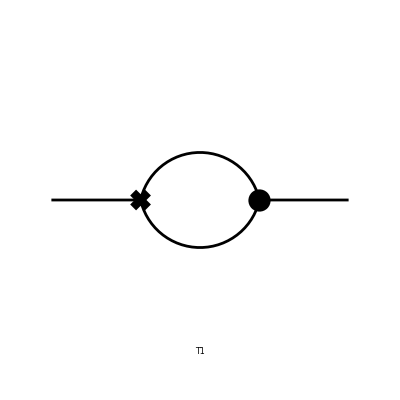

FeynArtsGraphics(1→1)(([T1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
Paint[OverlappedCorrectionA]
OverlappedCorrectionB=Take[Topology1LoopFermionicSelfEnergyCorrection,{20}];
Paint[OverlappedCorrectionB]
```

#### Field insertion

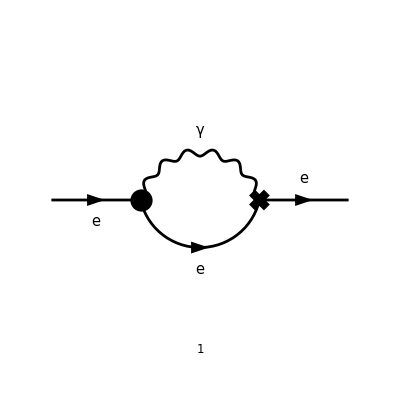

FeynArtsGraphics()(([1] | Null))

```mathematica
OverlappedCorrectionWITHFieldsA=InsertFields[OverlappedCorrectionA,Processee,ExcludeParticles->{S[_],V[2|3],(S|U)[_],F[3|4],F[2,{2|3}]}];
Paint[OverlappedCorrectionWITHFieldsA,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}]
```

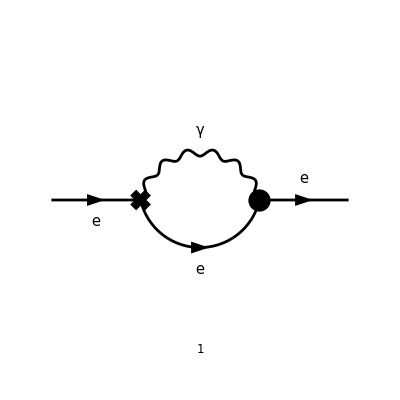

FeynArtsGraphics()(([1] | Null))

```mathematica
OverlappedCorrectionWITHFieldsB=InsertFields[OverlappedCorrectionB,Processee,ExcludeParticles->{S[_],V[2|3],(S|U)[_],F[3|4],F[2,{2|3}]}];
Paint[OverlappedCorrectionWITHFieldsB,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}]
```

#### Amplitudes

```mathematica
(*CT Overlapped A*)
```

```mathematica
FAamplAOCT=CreateFeynAmp[OverlappedCorrectionWITHFieldsA,Truncated->True,GaugeRules->{},PreFactor->1];
```

```mathematica
convertamplAOCT=FCFAConvert[FAamplAOCT,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{l},LorentzIndexNames->{μ,ν,α,β},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,DropSumOver->True,Contract->True,FinalSubstitutions->{Zm->SMP["Z_m"],Zpsi->SMP["Z_psi"],ZA->SMP["Z_A"],Zxi->SMP["Z_xi"],GaugeXi[V[1]]->1}];
convertamplAOCTmassless=convertamplAOCT//.SMP["m_e"]->0
```

(e^2 (γ̄)^ν.(γ̄·l̄).(γ̄)^ν)/((l̄)^2.(l̄-p̄)^2)-(e^2 Ze √Z_A Z_ψ (γ̄)^ν.(γ̄·l̄).(γ̄)^ν)/((l̄)^2.(l̄-p̄)^2)

```mathematica
AlgebraDiracmasslessCTAO1=DiracSimplify[convertamplAOCTmassless];
AlgebraDiracmasslessCTAO2=DiracSimplify[AlgebraDiracmasslessCTAO1]
```

(2 e^2 Ze √Z_A Z_ψ γ̄·l̄)/((l̄)^2.(l̄-p̄)^2)-(2 e^2 γ̄·l̄)/((l̄)^2.(l̄-p̄)^2)

```mathematica
{irrelevantmasslessIREGCTAO,loopsmasslessCTAO,THEUNIQUEIREGINTEGRALSmasslessCTAO}=FCLoopExtract[AlgebraDiracmasslessCTAO2,{l},loopHeadIREGmasslessCTAO];
IREGINTEGRALSEBmasslessCCTAO=THEUNIQUEIREGINTEGRALSmasslessCTAO/.loopHeadIREGmasslessCTAO->Identity
```

{(γ̄·l̄)/((l̄)^2.(l̄-p̄)^2)}

```mathematica
(*CT Overlapped B*)
```

```mathematica
FAamplBOCT=CreateFeynAmp[OverlappedCorrectionWITHFieldsB,Truncated->True,GaugeRules->{},PreFactor->1];
```

```mathematica
convertamplBOCT=FCFAConvert[FAamplBOCT,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{l},LorentzIndexNames->{μ,ν,α,β},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,DropSumOver->True,Contract->True,FinalSubstitutions->{Zm->SMP["Z_m"],Zpsi->SMP["Z_psi"],ZA->SMP["Z_A"],Zxi->SMP["Z_xi"],GaugeXi[V[1]]->1}];
convertamplBOCTmassless=convertamplBOCT//.SMP["m_e"]->0
```

(e^2 (γ̄)^ν.(γ̄·l̄).(γ̄)^ν)/((l̄)^2.(l̄-p̄)^2)-(e^2 Ze √Z_A Z_ψ (γ̄)^ν.(γ̄·l̄).(γ̄)^ν)/((l̄)^2.(l̄-p̄)^2)

```mathematica
AlgebraDiracmasslessCTBO1=DiracSimplify[convertamplBOCTmassless];
AlgebraDiracmasslessCTBO2=DiracSimplify[AlgebraDiracmasslessCTBO1]
```

(2 e^2 Ze √Z_A Z_ψ γ̄·l̄)/((l̄)^2.(l̄-p̄)^2)-(2 e^2 γ̄·l̄)/((l̄)^2.(l̄-p̄)^2)

```mathematica
{irrelevantmasslessIREGCTBO,loopsmasslessCTBO,THEUNIQUEIREGINTEGRALSmasslessCTBO}=FCLoopExtract[AlgebraDiracmasslessCTBO2,{l},loopHeadIREGmasslessCTBO];
IREGINTEGRALSEBmasslessCCTBO=THEUNIQUEIREGINTEGRALSmasslessCTBO/.loopHeadIREGmasslessCTBO->Identity
```

{(γ̄·l̄)/((l̄)^2.(l̄-p̄)^2)}

```mathematica
(*We need to evaluated this integrals... but it is the same as the overlapped C.T-A*)
```

#### Replacements

```mathematica
CTDTerm=DiracGamma[Momentum[l]]FeynAmpDenominator[PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l-p],0]]
```

(γ̄·l̄)/((l̄)^2.(l̄-p̄)^2)

```mathematica
(*What I computed by hand*)
```

```mathematica
CTDTermReplace=-DiracGamma[Momentum[p]]/2*(Ilogλ2-b*Log[-p^2/λ^2]+2*b)
```

-1/2 γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)

#### Substitution rule for the overlapped C.Ts

```mathematica
(*Substitution rule for the overlapped C.T-A*)
```

```mathematica
SubRuleforOverlappedCT={CTDTerm->CTDTermReplace};
```

```mathematica
(*The final electron bubble C.T*)
```

```mathematica
OverlappedCounterTermAFinal=AlgebraDiracmasslessCTAO2//.SubRuleforOverlappedCT
```

e^2 γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)-e^2 Ze √Z_A Z_ψ γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)

```mathematica
(*The renormalization constants and others IREG*)
```

```mathematica
(*The conventional definition*)
```

```mathematica
Z1=Ze Sqrt[SMP["Z_A"]]SMP["Z_psi"]
```

Ze √Z_A Z_ψ

```mathematica
Z2=1+SMP["e"]^2*SMP["d_psi"]
```

e^2 δ_ψ+1

```mathematica
NewRuleCTOverlapped={Z1->Z2};
```

```mathematica
(*Yes, remember also in QED Z1=Z2 to all orders*)
```

```mathematica
OverlappedCounterTermAFinal2=OverlappedCounterTermAFinal//.NewRuleCTOverlapped
```

e^2 γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)-e^2 (e^2 δ_ψ+1) γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)

```mathematica
OverlappedCounterTermAFinal3=Simplify[OverlappedCounterTermAFinal2]
```

e^4 δ_ψ γ̄·p̄ (b log(-p^2/λ^2)-2 b-Ilogλ2)

```mathematica
(*The final electron bubble C.T-B*)
```

```mathematica
OverlappedCounterTermBFinal=AlgebraDiracmasslessCTBO2//.SubRuleforOverlappedCT
```

e^2 γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)-e^2 Ze √Z_A Z_ψ γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)

```mathematica
OverlappedCounterTermBFinal2=OverlappedCounterTermBFinal//.NewRuleCTOverlapped
```

e^2 γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)-e^2 (e^2 δ_ψ+1) γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)

```mathematica
OverlappedCounterTermBFinal3=Simplify[OverlappedCounterTermBFinal2]
```

e^4 δ_ψ γ̄·p̄ (b log(-p^2/λ^2)-2 b-Ilogλ2)

### Renormalization

```mathematica
(*If everything is well, non-local terms should cancel*)
```

```mathematica
(*Before doing this, let's put some definitions for the counter-terms. All of them where taken for our Symmetry paper*)
```

```mathematica
CounterTermDeltaPsiQED=I*Ilogλ2
```

ⅈ Ilogλ2

(4 ⅈ Ilogλ2)/3

```mathematica
(*Now, the substitution rules*)
```

```mathematica
RuleCTField={SMP["d_psi"]->CounterTermDeltaPsiQED};
```

```mathematica
(*Re-writting the counterterm*)
```

```mathematica
OverlappedCounterTermAFinal4=OverlappedCounterTermAFinal3//.RuleCTField
```

ⅈ e^4 Ilogλ2 γ̄·p̄ (b log(-p^2/λ^2)-2 b-Ilogλ2)

```mathematica
OverlappedCounterTermBFinal4=OverlappedCounterTermBFinal3//.RuleCTField
```

ⅈ e^4 Ilogλ2 γ̄·p̄ (b log(-p^2/λ^2)-2 b-Ilogλ2)

```mathematica
(*Regulated Amplitude + Counter-Term*)
```

```mathematica
ChaveOverlapped=RegulatedEOverlappedAmplitudeIREG-OverlappedCounterTermAFinal4-OverlappedCounterTermBFinal4
```

ⅈ e^4 γ̄·p̄ (2 b Ilog2λ2+2 b Ilogλ2 log(-p^2/λ^2)-7 b Ilogλ2-2 Ilogλ2^2)-2 ⅈ e^4 Ilogλ2 γ̄·p̄ (b log(-p^2/λ^2)-2 b-Ilogλ2)

```mathematica
ChaveOverlapped2=Simplify[ChaveOverlapped]
```

ⅈ b e^4 (2 Ilog2λ2-3 Ilogλ2) γ̄·p̄